# Simple Frame Lorentz Transform

```mathematica
c=299.792458;
mp=938.27203;
mn=939.56536;
mF23=21423.094;
mF25=23294.025;
```

```mathematica
(* Tools *)
Angle[V_]:=If[V[[2]]==0 && V[[3]]==0,0,ArcTan[V[[3]],V[[2]]]]; 
Momentum[V_]:=Norm[{V[[2]],V[[3]]}] (* MeV/c *)
Mass[V_]:=√(V[[1]]^2-Momentum[V]^2);
KE[V_]:=V[[1]]-Mass[V];
Getβ[V_]:=Momentum[V]/V[[1]];
Getγ[V_]:=V[[1]]/Mass[V];
Lz[β_]:={{1/(√(1-β^2)),0,β/(√(1-β^2))},{0,1,0},{β/(√(1-β^2)),0,1/(√(1-β^2))}};
Jaco[pC_,β_]:=Module[{pA},pA=Lz[β].pC; (Momentum[pA])^3/(Momentum[pC])^2 (√(1-β^2))/(Momentum[pC]+pC[[1]] β pC[[3]]/Momentum[pC] )]
Jaco2[pC_,β_]:=Module[{pA},pA=Lz[β].pC; (Momentum[pA])^2/(Momentum[pC])^2 pC[[1]]/pA[[1]]]
Bρ2β[Bρ_, mass_,  Z_]:= √(1-mass^2/(mass^2+Bρ^2 c^2 Z^2))
TransForm[mass_,T_,θ_,β_]:=Lz[β].{mass+T, √(2 mass T+T^2)Sin[θ π/180], √(2 mass T+T^2)Cos[θ π/180]};
```

```mathematica
Manipulate[
NumberForm[{θ,180-Angle[TransForm[mp, Tc, θ,β]] 180/π},7],
{θ,0,180},
{{Tc,150},0,300},
{{β,-0.6465223},-1,1}]
```

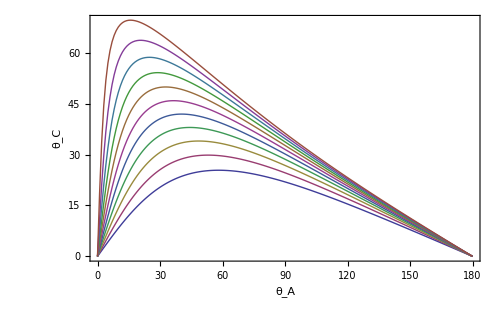

```mathematica
ListPlot[
Table[{θ,180-Angle[TransForm[mp, Tc, θ,-0.6465223]] 180/π},{Tc,60,260,20},{θ,0,180,1}],
PlotRange->All, Joined->True, Frame->True, FrameLabel->{"θ_A","θ_C"}, ImageSize->500]
```

```mathematica
Manipulate[
Graphics[{
{Gray,Arrow[{{0,-1000},{0,1000}}]},
{Gray,Arrow[{{-1000,0},{1000,0}}]},
{Red,Arrow[{{0,0},{ √(2 mp Tc+Tc^2)Sin[θ π/180], √(2 mp Tc+Tc^2)Cos[θ π/180]}}]},
{Pink, Circle[{0,0}, √(2 mp Tc+Tc^2)]},
{Blue,Arrow[{{0,0},TransForm[mp, Tc, θ,β][[2;;3]]}]},
{Cyan,Line[Table[TransForm[mp, Tc, θθ,β][[2;;3]],{θθ,-180,180,1}]]},
Text[θ,1.1{ √(2 mp Tc+Tc^2)Sin[θ π/180], √(2 mp Tc+Tc^2)Cos[θ π/180]}],
Text[180-Angle[TransForm[mp, Tc, θ,-0.6465223]] 180/π,1.1TransForm[mp, Tc, θ,β][[2;;3]]]
},
PlotRange->{{-1000,1000},{-2000,1000}}],
{{θ,20},-180,180},
{{Tc,150},0,300},
{{β,-0.6465223},-1,1}]
```

```mathematica
Manipulate[
ListPlot[
{Table[{180-Angle[TransForm[mp, Tc, θ,β]] 180/π,Jaco[{mp+Tc, √(2 mp Tc+Tc^2)Sin[θ π/180], √(2 mp Tc+Tc^2)Cos[θ π/180]},β]},{θ,0,180,1}],
Table[{180-Angle[TransForm[mp, Tc, θ,β]] 180/π,Jaco2[{mp+Tc, √(2 mp Tc+Tc^2)Sin[θ π/180], √(2 mp Tc+Tc^2)Cos[θ π/180]},β]},{θ,0,180,1}]
},
Joined->True
],
{{Tc,150},0,300},
{{β,-0.6465223},-1,1}]
```